```mathematica
(* Plotting Package*)
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,amsbsy}"}];
rasterListContourPlot[pList_,opts:OptionsPattern[]]:=Module[{img,cont,contL,plotRangeRule,contourOptions,frameOptions,rangeCoords},contourOptions=Join[FilterRules[{opts},FilterRules[Options[ListContourPlot],Except[{Background,Frame,Axes}]]],{Frame->None,Axes->None}];
contL=ListContourPlot[pList,Evaluate@Apply[Sequence,contourOptions]];
cont=First[Cases[{contL},Graphics[__],Infinity]];
img=Rasterize[Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,1]]],PlotRangePadding->None,ImagePadding->None,Options[cont,PlotRange]],"Image",ImageSize->With[{size=Total[{2,0} (ImageSize/.{opts})/.{ImageSize->CurrentValue[ImageSize]}]},If[NumericQ[size],size,First[WindowSize/.Options[EvaluationNotebook[]]]]]];
plotRangeRule=FilterRules[AbsoluteOptions[cont],PlotRange];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
If[Head[contL]===Legended,Legended[#,contL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,2]]]],Evaluate@Apply[Sequence,frameOptions]]]
Clear[undistortedGraphicsColumn];
Options[undistortedGraphicsColumn]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsColumn[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,width, xsizes, ysizes},width=Max@sizes[[All,1]];
ysizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@list-1]];
xsizes = sizes[[All, 1]];
Graphics[Table[Inset[list[[i]],{(width - xsizes[[i]]) / 2,-Plus@@ysizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{width,Plus@@ysizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@ysizes,0}},AspectRatio->Plus@@ysizes/width,PlotRangePadding->None]]

Clear[undistortedGraphicsRow];
Options[undistortedGraphicsRow]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsRow[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,height, xsizes, ysizes},height=Max@sizes[[All,2]];
xsizes=sizes[[All,1]]+Join[ConstantArray[OptionValue[Spacings],Length@list-1],{0}];
ysizes = sizes[[All, 2]];
Graphics[Table[Inset[list[[i]],{If[i>1, Plus@@xsizes[[;;i-1]],0], (height-ysizes[[i]])/2},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{Plus@@xsizes, height},ImagePadding->None,PlotRange->{{0, Plus@@xsizes}, {0, height}},AspectRatio->height/(Plus@@xsizes),PlotRangePadding->None]]

Clear[format]
Options[format] = Options[PaddedForm];
format[x_, sd_]:=Module[{m,e},
{m,e} = MantissaExponent[x];
If[x == 0, "0",If[-2≤e≤2,ToString[PaddedForm[x, sd]],ToString[PaddedForm[ToExpression[ToString[m]]*10, sd]]<>"\\times10^{"<>ToString[e-1]<>"}"]]
]
```

```mathematica
ρ=Compile[{{x1,_Real},{x2,_Real}},{(2 √(3/241) ⅇ^(-(2 (17 x1^2-44 x1 x2+71 x2^2))/6025))/(25 π)}];
j=Compile[{{x1,_Real},{x2,_Real}},{(18 √(3/241) ⅇ^(-(2 (17 x1^2-44 x1 x2+71 x2^2))/6025) (22 x1-71 x2))/(6025 π),(18 √(3/241) ⅇ^(-(2 (17 x1^2-44 x1 x2+71 x2^2))/6025) (17 x1-22 x2))/(6025 π)}];
σ=Compile[{{x1,_Real},{x2,_Real}},{(81 √(3/241) ⅇ^(-(2 (17 x1^2-44 x1 x2+71 x2^2))/6025) (14 x1^2-44 x1 x2+41 x2^2))/(753125 π)}];
```

```mathematica
xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
h = {100.,40.}/199.;
points = N[Table[{x, y}, {x, xmin, xmax, h[[1]]}, {y, ymin, ymax, h[[2]]}]];
fpoints = Round[Flatten[points, 1],h[[2]]/400000];
sqrtpts = Sqrt[Length[fpoints]];
sqrtplaquettes=sqrtpts-1;
plaquettes =Table[{i, i}, {i,1,sqrtplaquettes*sqrtplaquettes}];
sqrtverticescurrents = sqrtpts - 2;
vertices =Table[{i, i}, {i,1,sqrtverticescurrents*sqrtverticescurrents}];
```

```mathematica
Anaplaquettecurrents = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);

xcur=j[xcoord,ycoord][[1]];
ycur=j[xcoord,ycoord][[2]];

{{xcoord, ycoord},{xcur, ycur}},
{pedge, plaquettes}
];
Anaplaquettedissipations = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);

val=σ[xcoord,ycoord][[1]];

{xcoord, ycoord,val},
{pedge, plaquettes}
];
Anadensities = Table[

xcoord = point[[1]];
ycoord = point[[2]];

rho=ρ[xcoord,ycoord][[1]];

{xcoord, ycoord,rho},
{point, fpoints}
];
Anaplaquettedissipations = Chop[Anaplaquettedissipations];
```

```mathematica
cmapdensity = (Blend[{RGBColor[{255, 247, 243}/255],RGBColor[{145, 0, 63}/255]}, #]&);
mind= Round[Min[Transpose[Anadensities][[-1]]]];
maxd = Max[Transpose[Anadensities][[-1]]];

ticklocationsd = N[FindDivisions[{mind, maxd}, 5]];

mind = ticklocationsd[[1]];
maxd = ticklocationsd[[-1]];
stepd = (maxd - mind) /10.;
cmapdensity2 = cmapdensity[(#-mind) / (10.*stepd)]&;
ymin=-20;
ymax=20;
xmin=-50;
xmax=50;
xmajor=20;
xminor=0.1;
ymajor=8;
yminor=0.1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,MaTeX[i, FontSize->14],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->14],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdensities = Show[
rasterListContourPlot[Anadensities,
ColorFunction->cmapdensity2,
PlotRange->Full,
ColorFunctionScaling->False
],
Frame->True,
FrameStyle-> Transparent,
FrameTicks->ft,
FrameLabel->{MaTeX["x_1",FontSize->18],MaTeX["x_2",FontSize->18]},
ImageSize->250,
AspectRatio->1,
ImagePadding->{{60, 10}, {50, 10}}
]
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

-Graphics-

```mathematica
ticklabelsd=MaTeX[format[#,{2,3}], FontSize->14]&/@ticklocationsd;
densitycolorbar = Graphics[
Table[Inset[ticklabelsd[[i]],Scaled[{((0.8-0.1)/(Length[ticklocationsd]-1))(i-1) + 0.25,0.7}]], {i, 1, Length[ticklocationsd]}],
ImageSize->{250, 75},
Epilog->Inset[
BarLegend[{cmapdensity2, {mind, maxd}},
LegendLayout->"Row",
LegendMarkerSize->{207, 30},
"Ticks"->ticklocationsd,
"TickLabels"->(""&/@ticklocationsd),
"TicksStyle"->Directive[Opacity[1],Black,FontColor->Black,AbsoluteThickness[3]],
"TickSide"->Left,
Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}]/.AbsoluteThickness[_]->AbsoluteThickness[2],
Scaled[{0, 0}], Scaled[{-0.15, 0.05}]
],
Prolog->{Text[MaTeX["\\rho_{\\rm ss}(\\mathbf{x})", FontSize->18],Scaled[{0.15, 0.35}]]},
AspectRatio->Full
]
```

-Graphics-

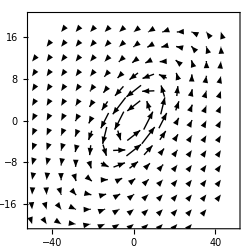

```mathematica
cmapcurrent = (Blend[{RGBColor[{0, 0, 0}/255], RGBColor[{0, 0, 0}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[Anaplaquettecurrents][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[Anaplaquettecurrents][[-1]])];


ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapcurrent2 = cmapcurrent[(#-minc) / (10.*stepc)]&;
ymin=-20;
ymax=20;
xmin=-50;
xmax=50;
xmajor=20;
xminor=0.1;
ymajor=8;
yminor=0.1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,MaTeX[i, FontSize->14],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->14],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localcurrents = Show[
ListVectorPlot[Anaplaquettecurrents,
PlotRange->{{xmin, xmax}, {ymin, ymax}},
VectorColorFunction->(cmapcurrent2[#5]&),
VectorColorFunctionScaling->False,
VectorScale->{0.07, Automatic,#5&},
VectorPoints->{15,15}
],
Frame->True,
FrameStyle-> Transparent,
(*FrameTicks->ft,*)
(*FrameLabel->{MaTeX["x_1",FontSize->18],MaTeX["x_2",FontSize->18]},*)
ImageSize->250,
AspectRatio->1,
ImagePadding->{{60, 10}, {50, 10}}]
```

```mathematica
cmap = ColorData["M10DefaultDensityGradient"];
minv = Min[Transpose[Anaplaquettedissipations][[-1]]];
maxv = Max[Transpose[Anaplaquettedissipations][[-1]]];

ticklocations = N[FindDivisions[{minv, maxv}, 5]];

minv = ticklocations[[1]];
maxv = ticklocations[[-1]];
stepv = (maxv - minv) /10.;
cmap2 = cmap[(#-minv) / (10.*stepv)]&;

ymin=-20;
ymax=20;
xmin=-50;
xmax=50;
xmajor=20;
xminor=0.1;
ymajor=8;
yminor=0.1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,MaTeX[i, FontSize->14],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,(*MaTeX[j, FontSize->14]*),{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdissipationrate = Show[
rasterListContourPlot[Anaplaquettedissipations,
(*PlotLegends->True,*)
PlotRange->{{xmin, xmax}, {ymin, ymax},{minv,maxv}},
ColorFunctionScaling->False,
ColorFunction->cmap2,
ClippingStyle->Automatic,
Contours->6
],
FrameStyle->Transparent,
FrameTicks->ft,
FrameLabel->{MaTeX["x_1",FontSize->18](*,MaTeX["x_2",FontSize->14]*)},
ImageSize->250,
AspectRatio->1,
ImagePadding->{{60, 10}, {50, 10}},
Epilog->{
Inset[Text[MaTeX["{\\rm}\\color{white} \\dot S_{\\rm ss} = \\int d \\mathbf{x}\\\ \\dot \\sigma_{\\rm ss}(\\mathbf{x})", FontSize->17]], Scaled[{0.62, 0.12}]]}
]
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

-Graphics-

```mathematica
ticklabels=MaTeX[format[#,{2,3}], FontSize->14]&/@ticklocations;
dissipationcolorbar = Graphics[
Table[Inset[ticklabels[[i]],Scaled[{((0.8-0.1)/(Length[ticklocationsd]-1))(i-1) + 0.3,0.7}]], {i, 1, Length[ticklocations]}],
ImageSize->{250, 75},
Epilog->Inset[
BarLegend[{cmap2, {minv, maxv}},
LegendLayout->"Row",
LegendMarkerSize->{207, 30},
"Ticks"->ticklocations,
"TickLabels"->(""&/@ticklocations),
"TicksStyle"->Directive[Opacity[1],Black,FontColor->Black,AbsoluteThickness[3]],
"TickSide"->Left,
Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}]/.AbsoluteThickness[_]->AbsoluteThickness[2],
Scaled[{0, 0}], Scaled[{-0.15, 0.05}]
],
Prolog->{Text[MaTeX["\\dot \\sigma_{\\rm ss}(\\mathbf{x})", FontSize->18],Scaled[{0.18, 0.3}]]},
AspectRatio->Full
]
```

-Graphics-

```mathematica
density=Show[localdensities,localcurrents,
Epilog->{
Inset[
(*Text[MaTeX["\\boldsymbol{j}^\\pi(\\boldsymbol{x})", FontSize->16]*)
Framed[
undistortedGraphicsColumn[
{Graphics[
Text[MaTeX["\\mathbf{j}_{\\rm ss}(\\mathbf{x})", FontSize->18]],
ImageSize->{40, 20}
],
Graphics[{Arrowheads[0.3],Thick,Arrow[{{0, 0}, {1, 0}}]}, ImageSize->{36, 18}, AspectRatio->18/36]
},
Spacings->-8
],
RoundingRadius->11
],
Scaled[{0.84, 0.13}]
]
}
]
```

-Graphics-

```mathematica
densityfig=undistortedGraphicsColumn[{densitycolorbar,density}]
```

-Graphics-

```mathematica
dissfig=undistortedGraphicsColumn[{ dissipationcolorbar,localdissipationrate}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"densityfig.pdf", densityfig];
Export[NotebookDirectory[]<>"dissfig1.pdf", dissfig];
```